# Linear Algebra

Clarisa Leu-Rodriguez

The Basics

## Problem 1

2 I_1-1 I_2+3 I_3+4 I_4=9
1 I_1+0 I_2-2 I_3+7 I_4=11
3 I_1-3 I_2+1 I_3+5 I_4=8
2 I_1+1 I_2+4 I_3+4 I_4=10

In linear algebra, a linear system of equations can also be represented as an augmented matrix. The augmented matrix of the linear system shown above is:

```mathematica
MatrixForm[A = {
{2,-1,3,4,9},
{1,0,-2,7,11},
{3,-3,1,5,8},
{2,1,4,4,10}
}
]
```

Finding the reduced row echelon form for the augmented matrix, we can directly solve for I_1, I_2, I_3, and I_4.

```mathematica
MatrixForm[B = RowReduce[A]]
```

Therefore, I_1=-1, I_2=0, I_3=1, and I_4=2. The system of linear equations can also be put into a list and solved directly:

```mathematica
linearSystemProb1 = {
2I2-1I2+3I3+3I4==9,
1I1-2I3+7I4==11,
3I1-3I2+1I3+5I4==8,
2I1+1I2+4I3+4I4==10
}
```

Solving the linear system for variables I_1, I_2, I_3, and I_4:

```mathematica
solutionsProb1 = Solve[linearSystemProb1,{I1,I2,I3,I4}]
```

To check our solutions, we can simply use the /. operation and see if the solutions yielded are the true solutions to the linear system when replaced into the original equations.

```mathematica
linearSystemProb1/.solutionsProb1
```

In conclusion:

I_1=-1
I_2=0
I_3=1
I_4=2

## Problem 2

For a cubic interpolating polynomial going through four points: 
[Given: (0,10), (1,7), (3,-11), (4,-14)]; in the form f(x)= ax^3+bx^2+cx+d, 
coefficients a, b, c, and d can be found using matrices. 
Finding expressions for f(0), f(1), f(3), and f(4); the four points on our function can be represented as a linear system of equations:

0a+0b+0c+1d=10     //f(0)
1a+1b+1c+1d=7         //f(1)
27a+9b+3c+1d=-11     //f(3)
64a+16b+4c+1d=-14       //f(4)

The augmented matrix of the linear system is:

```mathematica
MatrixForm[F={
{0,0,0,1,10},
{1,1,1,1,7},
{27,9,3,1,-11},
{64,16,4,1,-14}
}
]
```

To directly solve for variables a, b, c, and d, we can row reduce matrix F:

```mathematica
MatrixForm [G=RowReduce[F]]
```

```mathematica
solutionsProb2 = {a->1,b->-6,c->2,d->10}
```

Defining our linear system, we can check our solution set and see that it satisfies the equations using the /. operator.

```mathematica
linearSystemProb2 = {
d==10,
a+b+c+d==7,
27a+9b+3c+d==-11,
64a+16b+4c+d==-14
}
```

```mathematica
linearSystemProb2/.solutionsProb2
```

Our solutions to the linear equations are correct. a=1, b=-6, c=2, and d=10. 
Defining our function in a variable and being given the graph of the interpolating polynomial we can also check our work via the graphical method. 
To do this, we will graph our points on our function and confirm that they line up. Using tooltip, the points on the graph when hovered upon will show. Epilog allows 2D graphic primitives to be applied to our plot.

```mathematica
f[x_]:=x^3-6 x^2+2 x+10
```

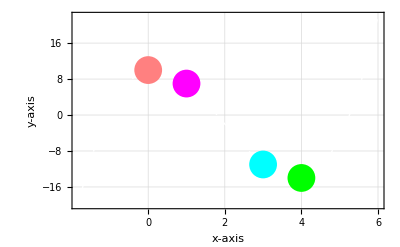

```mathematica
Plot[f[x],{x,-2,6},
Epilog->{PointSize[0.05],Magenta,Tooltip[#,#] &@Point[{1,f[1]}],
Cyan,Tooltip[#,#]&@Point[{3,f[3]}],
Green,Tooltip[#,#]&@Point[{4,f[4]}],
Pink,Tooltip[#,#]&@Point[{0,f[0]}]},
AxesStyle->Directive[White,Dashed],
PlotRange->{Automatic,{-20,All}},
PlotRangePadding->{None,{0,Scaled[0.1]}},
Frame->True,GridLines->Automatic,
FrameLabel->(Style[#,Bold,FontSize->18]&/@{"x-axis","y-axis"}),
PlotStyle->{White,Dashed,Thick}]
```

Checking the solutions via the graphical method and seeing that all of the points lie on the function. We can conclude that:

a = 1
b = -6
c = 2
d = 10

## Problem 3

For the following matrices P,Q,R defined below, Mathematica will allow us to perform several different matrix operations. 
Primarily, using the transpose and trace function:

```mathematica
P = ({{3, 0}, {-1, 2}, {1, 1}})  
Q=({{4, -1}, {0, 2}})
R = ({{1, 4, 2}, {3, 1, 5}})
```

### A.) 2 P^T-R

2*Transpose of Matrix P - Matrix R :

```mathematica
MatrixForm[2*Transpose[P]-R]
```

### B.) Tr(QR)

Trace of Matrix (Q*R) :

```mathematica
MatrixForm[Tr[Q.R]]
```

### C.) R(PQ)

Matrix R*(Matrix P*Matrix Q) :

```mathematica
MatrixForm[R.(P.Q)]
```

### D.) RR^T

Matrix R*Transpose of Matrix R :

```mathematica
MatrixForm[resultD = R.Transpose[R]]
```

### E.) Q^T(RR^T-P^TP)

Transpose of Matrix Q*(Matrix R*Transpose of Matrix R - Transpose of Matrix P*Matrix P) :

```mathematica
MatrixForm[Transpose[Q].(resultD-(Transpose[P].P))]
```